# Ball Triangle Picking

### Author

Eric W. Weisstein
March 14, 2017

This notebook downloaded from http://mathworld.wolfram.com/notebooks/ComputationalGeometry/BallTrianglePicking.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/BallTrianglePicking.html.

©2017 Wolfram Research, Inc. except for portions noted otherwise

## Area of a Random Triangle

```mathematica
TriangleArea3D[{{x1_,y1_,z1_},{x2_,y2_,z2_},{x3_,y3_,z3_}}]:=Sqrt[(-x2*y1+x3*y1+x1*y2-x3*y2-x1*y3+x2*y3)^2+(x2*z1-x3*z1-x1*z2+x3*z2+x1*z3-x2*z3)^2+(-y2*z1+y3*z1+y1*z2-y3*z2-y1*z3+y2*z3)^2]/2
```

### Exact Mean

```mathematica
9/77 π//N
```

0.367199

### RandomPoint

```mathematica
tri=RandomPoint[Ball[],{10^6,3}];//Timing
```

{0.256386,Null}

```mathematica
Length[areas=Abs[TriangleArea3D/@tri]]//Timing
```

{12.0898,1000000}

```mathematica
TimeConstrained[Length[areas=Area[Triangle[#]]&/@tri],60]//Timing
```

{60.3168,$Aborted}

```mathematica
TimeConstrained[Length[areas=RegionMeasure[Triangle[#]]&/@tri],60]//Timing
```

{60.2907,$Aborted}

bug(330535): Area, Volume, and RegionMeasure should be faster on shape primitives

```mathematica
Through[{Mean,Variance}[areas]]
```

{0.367281,0.0450954}

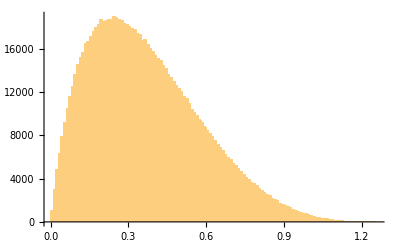

```mathematica
Histogram[areas,100]
```

### Monte Carlo

#### 10^7

```mathematica
Length[pts3=Select[2Table[Random[],{10^7},{3}]-1,Norm[#]<1&]]//Timing
```

{53.8915,5235672}

```mathematica
Length[tris3=Partition[pts3,3]]
```

1745224

```mathematica
Mean[data=TriangleArea3D/@tris3]//Timing
```

{35.3364,0.368213}

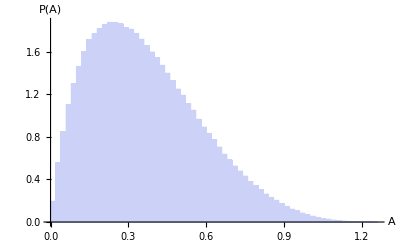

```mathematica
Histogram[data,{.02},"PDF",AxesLabel->{A,P[A]}]
```

#### 10^8

```mathematica
Length[pts3=Select[2Table[Random[],{10^8},{3}]-1,Norm[#]<1&]]//Timing
```

{614.12,52357543}

```mathematica
Length[tris3=Partition[pts3,3]]
```

17452514

```mathematica
Mean[data=TriangleArea3D/@tris3]//Timing
```

{371.581,0.368013}

```mathematica
MaxMemoryUsed[]/10^9.GB
```

36.8413 GB

## Probability of Obtaining an Acute Triangle

### Monte Carlo

#### 2-D

```mathematica
N[Count[Triangle/@tris,_?ObtuseQ]/Length[tris],10]//Timing
```

{52.98 Second,0.7195589297}

```mathematica
1-Last[%]
```

0.28044107

Exact value is supposed to be P_2= 4/π^2-1/8≈0.280285.

#### 3-D

```mathematica
N[Count[Triangle@@@Polygon2D/@tris3,_?ObtuseQ]/Length[tris3],10]//Timing
```

{116.97 Second,0.5263712718}

```mathematica
1-Last[%]
```

0.473628728

Exact value is supposed to be P_3= 33/70≈0.471429.

### Exact

```mathematica
p[n_Integer?OddQ]:=Module[{m=(n-1)/2,k},
m Binomial[2m,m]^2 2^(2m) Sum[Binomial[2k,k](3m+k+1)/(m+k)/(4m+2k+1)/Binomial[2m+k,m]/Binomial[4m+2k,2m+k],{k,0,m}]-1/2-2^(2m-1) Binomial[2m,m]Binomial[4m,2m]/Binomial[4m,m]/Binomial[6m+1,2m]
]

p[n_Integer?EvenQ]:=Module[{m=(n-2)/2,k},
2^(4m)/Binomial[2m,m]/Pi^2 (Sum[2^(2k)(3m+k+3)/Binomial[2k,k]/(2k+1)/Binomial[2m+k,m]/Binomial[2m+k+2,2],{k,0,m}]+1/(2m+1)^2/Binomial[2m,m])+1/4-3/2^(2m+4)Binomial[4m+4,m+1]/Binomial[2m+2,m+1]
]
```

### Plot

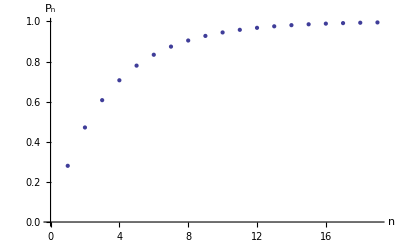

```mathematica
ListPlot[Table[p[n],{n,2,20}],AxesLabel->{n,Subscript[P,n]}]
```

### Values

```mathematica
Table[{n,p[n]},{n,2,10}]//ColumnForm//TraditionalForm
```

{2,-1/8+4/π^2}
{3,33/70}
{4,1/32+256/(45 π^2)}
{5,1415/2002}
{6,31/256+2048/(315 π^2)}
{7,231161/277134}
{8,89/512+4194304/(606375 π^2)}
{9,9615369/10623470}
{10,1469/7168+54525952/(7640325 π^2)}

```mathematica
N[%]
```

{0.280285,0.471429,0.607655,0.706793,0.779842,0.834113,0.874668,0.905106,0.928027}

### Explicit

Even

```mathematica
FullSimplify[With[{m=(n-2)/2},
2^(4m)/Binomial[2m,m]/Pi^2 (Sum[2^(2k)(3m+k+3)/Binomial[2k,k]/(2k+1)/Binomial[2m+k,m]/Binomial[2m+k+2,2],{k,0,m}]+1/(2m+1)^2/Binomial[2m,m])+1/4-3/2^(2m+4)Binomial[4m+4,m+1]/Binomial[2m+2,m+1]],n∈Integers&&n>0&&Mod[n,2]==0]
```

1/4-(3 2^(-2-n) Binomial[4+2 (-2+n),1+1/2 (-2+n)])/Binomial[n,1+1/2 (-2+n)]+(2^(2 (-2+n)) (1/((-1+n)^2 Binomial[-2+n,1/2 (-2+n)])+2 (-(2^(1-n) √π Gamma[n/2] HypergeometricPFQ[{1,1,n/2},{1/2,n},1])/((-3+2 n) Gamma[1/2+n/2])-(2^-n n √π Gamma[n/2] HypergeometricPFQ[{1,1,n/2},{1/2,n},1])/((-3+2 n) Gamma[1/2+n/2])+(3 2^(4-n) √π Gamma[1+n/2] HypergeometricPFQ[{1,1,n/2},{3/2,-1+n},1])/((3-8 n+4 n^2) Gamma[-1/2+n/2])-(2^(3-n) √π Gamma[n/2] HypergeometricPFQ[{1,1,n/2},{3/2,-1+n},1])/((3-8 n+4 n^2) Gamma[-1/2+n/2])+(2^n Gamma[1+n/2]^3 HypergeometricPFQ[{1,1+n/2,n},{1/2+n/2,(3 n)/2},1])/(n (-3+2 n) Gamma[(3 n)/2])+(2^n Gamma[1+n/2]^2 Gamma[n/2] HypergeometricPFQ[{1,1+n/2,n},{1/2+n/2,(3 n)/2},1])/(n (-3+2 n) Gamma[(3 n)/2])-(3 2^(1+n) Gamma[1+n/2]^2 Gamma[n/2] HypergeometricPFQ[{1,1+n/2,n},{3/2+n/2,-1+(3 n)/2},1])/((3-5 n-4 n^2+4 n^3) Gamma[-1+(3 n)/2])+(2^n Gamma[1+n/2] Gamma[n/2]^2 HypergeometricPFQ[{1,1+n/2,n},{3/2+n/2,-1+(3 n)/2},1])/((3-5 n-4 n^2+4 n^3) Gamma[-1+(3 n)/2])+(2^(-1-n) √π Gamma[n/2] (-HypergeometricPFQ[{1,1,n/2},{1/2,1+n},1]+n^2 HypergeometricPFQ[{1,1,n/2},{1/2,1+n},1]+n HypergeometricPFQ[{2,2,1+n/2},{3/2,2+n},1]))/((-1+2 n) Gamma[3/2+n/2])-(2^(-3+n) Gamma[1+n/2]^2 Gamma[n/2] (-4 HypergeometricPFQ[{1,1+n/2,n},{1/2+n/2,1+(3 n)/2},1]-4 n HypergeometricPFQ[{1,1+n/2,n},{1/2+n/2,1+(3 n)/2},1]+9 n^2 HypergeometricPFQ[{1,1+n/2,n},{1/2+n/2,1+(3 n)/2},1]+9 n^3 HypergeometricPFQ[{1,1+n/2,n},{1/2+n/2,1+(3 n)/2},1]+8 n HypergeometricPFQ[{2,2+n/2,1+n},{3/2+n/2,2+(3 n)/2},1]+4 n^2 HypergeometricPFQ[{2,2+n/2,1+n},{3/2+n/2,2+(3 n)/2},1]))/((-1+n+2 n^2) Gamma[2+(3 n)/2]))))/(π^2 Binomial[-2+n,1/2 (-2+n)])

Odd

```mathematica
(expr=FullSimplify[With[{m=(n-1)/2},
m Binomial[2m,m]^2 2^(2m) Sum[Binomial[2k,k](3m+k+1)/(m+k)/(4m+2k+1)/Binomial[2m+k,m]/Binomial[4m+2k,2m+k],{k,0,m}]-1/2-2^(2m-1) Binomial[2m,m]Binomial[4m,2m]/Binomial[4m,m]/Binomial[6m+1,2m]],
n∈Integers&&n>0&&Mod[n,2]==1
])//TraditionalForm
```

1/4 ((2^(2 n-3) (n-1) n (Γ(n/2))^4 (n _3(F̃)_2(1,n+1,(n+2)/2;(n+3)/2,(3 n)/2+1;1)-2 _3(F̃)_2(1,n,(n+2)/2;(3 n)/2,(n+3)/2;1)))/π^(3/2)-(4^(1-n) √π Γ(2 n))/(Γ((3 n)/2) Γ((n+1)/2))+4)

However, this expression is valid for all n, not just odd

```mathematica
expr=1/4 (4-(4^(1-n) √π Gamma[2 n])/(Gamma[(3 n)/2] Gamma[(1+n)/2])+1/π^(3/2)(2^(-3+2 n) (-1+n) n Gamma[n/2]^4 (-2 HypergeometricPFQRegularized[{1,n,(2+n)/2},{(3 n)/2,(3+n)/2},1]+n HypergeometricPFQRegularized[{1,1+n,(2+n)/2},{(3+n)/2,1+(3 n)/2},1])));
```

```mathematica
v=Table[expr,{n,9}];
```

```mathematica
N[v]
```

{Indeterminate,0.280285,0.471429,0.607656,0.706793,0.779847,0.834113,0.874402,0.905106}

```mathematica
FullSimplify[v]//ColumnForm
```

Indeterminate
-1/8+4/π^2
33/70
(1125 π^2+128 (59-60 HypergeometricPFQ[{1,1,2},{3/2,4},1]+15 HypergeometricPFQ[{1,1,3},{3/2,5},1]))/(1440 π^2)
1415/2002
223/256+(64 (153-140 HypergeometricPFQ[{1,1,3},{3/2,6},1]+35 HypergeometricPFQ[{1,1,4},{3/2,7},1]))/(1575 π^2)
231161/277134
473/512+(65536 (-3 HypergeometricPFQ[{1,5,8},{11/2,12},1]+HypergeometricPFQ[{1,5,9},{11/2,13},1]))/(779625 π^2)
9615369/10623470